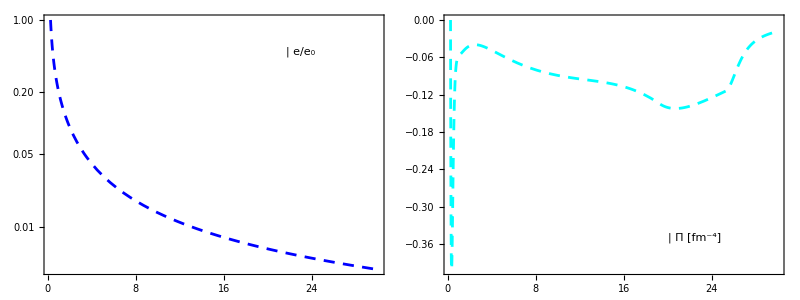

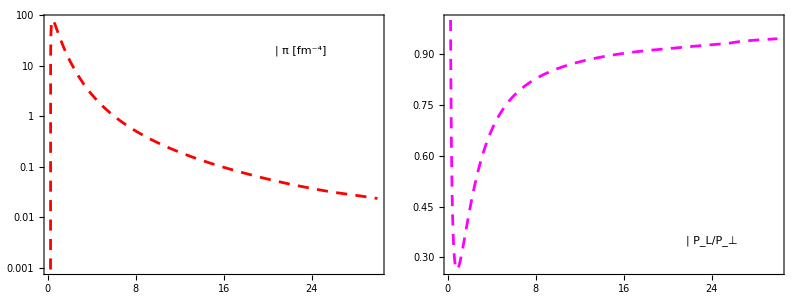

```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

styles={Directive[RGBColor[0,0.0,1.0],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[RGBColor[1,0,0],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],
Directive[RGBColor[0,1,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]]};

EnergyDensityDataRaw=Import[wd<>"/eplot.dat"];
piDataRaw=Import[wd<>"/piplot.dat"];
PiDataRaw=Import[wd<>"/bulkplot.dat"];
plptDataRaw=Import[wd<>"/plptplot.dat"];

piNSDataRaw=Import[wd<>"/piNSplot.dat"];
PiNSDataRaw=Import[wd<>"/bulkNSplot.dat"];
plptNSDataRaw=Import[wd<>"/plptNSplot.dat"];

EnergyDensityData= Take[EnergyDensityDataRaw,{2,Length[EnergyDensityDataRaw]}];
piData= Take[piDataRaw,{2,Length[piDataRaw]}];
PiData= Take[PiDataRaw,{2,Length[PiDataRaw]}];
plptData= Take[plptDataRaw,{2,Length[plptDataRaw]}];

piNSData= Take[piNSDataRaw,{2,Length[piNSDataRaw]}];
PiNSData= Take[PiNSDataRaw,{2,Length[PiNSDataRaw]}];
plptNSData= Take[plptNSDataRaw,{2,Length[plptNSDataRaw]}];

t0 = EnergyDensityData[[1,1]];
tf = EnergyDensityData[[Length[EnergyDensityData],1]];

energydensity = Interpolation[EnergyDensityData[[All,{1,2}]]];
pi = Interpolation[piData[[All,{1,2}]]];
bulk = Interpolation[PiData[[All,{1,2}]]];
plpt = Interpolation[plptData[[All,{1,2}]]];

piNS = Interpolation[piNSData[[All,{1,2}]]];
bulkNS = Interpolation[PiNSData[[All,{1,2}]]];
plptNS = Interpolation[plptNSData[[All,{1,2}]]];

legend1=Panel[Grid[{{Graphics[{styles[[1]],Line[{{0,0},{1,0}}]},ImageSize->43,AspectRatio->0.2],Style["e/e_0",FontSize->18,FontFamily->"Times"]}}],Background->White];

legend2=Panel[Grid[{{Graphics[{styles[[2]],Line[{{0,0},{1,0}}]},ImageSize->43,AspectRatio->0.2],Style["π [fm^-4]",FontSize->18,FontFamily->"Times"]}}],Background->White];

legend3=Panel[Grid[{{Graphics[{styles[[3]],Line[{{0,0},{1,0}}]},ImageSize->43,AspectRatio->0.2],Style["Π [fm^-4]",FontSize->18,FontFamily->"Times"]}}],Background->White];

legend4=Panel[Grid[{{Graphics[{styles[[4]],Line[{{0,0},{1,0}}]},ImageSize->43,AspectRatio->0.2],Style["P_L/P_⊥",FontSize->18,FontFamily->"Times"]}}],Background->White];

energyplot=LogPlot[{energydensity[t]},{t,t0,tf},PlotRange->All,PlotStyle->styles[[1]],ImageSize->320,Frame->True,Axes->False,BaseStyle->{FontSize->16},AspectRatio->0.75,Epilog->Inset[legend1,{23,-0.7}]];
bulkplot = Plot[{bulk[t]},{t,t0,tf},PlotRange->All,PlotStyle->{styles[[3]]},ImageSize->320,Frame->True,Axes->False,BaseStyle->{FontSize->16},AspectRatio->0.75,Epilog->Inset[legend3,{22.5,-0.35}]];
piplot = LogPlot[{pi[t]},{t,t0,tf},PlotRange->All,PlotStyle->{styles[[2]]},ImageSize->320,Frame->True,Axes->False,FrameLabel->{"τ (fm/c)"},BaseStyle->{FontSize->16},AspectRatio->0.75,Epilog->Inset[legend2,{23,3}]];
plptplot = Plot[{plpt[t]},{t,t0,tf},PlotRange->All,PlotStyle->{styles[[4]]},ImageSize->320,Frame->True,Axes->False,FrameLabel->{"τ (fm/c)"},BaseStyle->{FontSize->16},AspectRatio->0.75,Epilog->Inset[legend4,{24,0.35}]];

a1=Grid[{{energyplot,bulkplot}}]
a2=Grid[{{piplot,plptplot}}]
```

```mathematica
Export["vhydro.pdf",Grid[{{a1},{a2}}]]
```

vhydro.pdf